# Práctica 2.2

Alumno: Adrián Martínez Martínez

## Actividad 1

```mathematica
AFDtoAC[AFD_]:=Module[{Q,Σ,δ,S,i, sol,j, CharColorRules, aux},
Q=AFD[[1]];
Σ=AFD[[2]];
δ=AFD[[3]];
S=Union[Q,Σ];
sol={S};
CharColorRules = {f->White};
PrependTo[sol[[1]],f];

(* Si no es unidireccional, devuelve False *)
If[Length[δ[[1]]]!=3, Return[False]];

For[i=1,i<=Length[S],i++,
	AppendTo[sol,{S[[i]]}];
	AppendTo[CharColorRules, S[[i]]-> ColorData[2,i]];
	For[j=1,j<=Length[S],j++,
	AppendTo[sol[[i+1]],_]
];
];

For[i=1,i<=Length[S],i++,
For[j=1,j<=Length[S],j++,
aux = Cases[δ, {S[[i]],S[[j]],_}];
If[Length[aux] > 0,
(*Then*)
sol[[i+1,j+1]] = aux[[1,3]],
(*Else*)

(*Si ambos elementos son un símbolo del alfabeto o ambos son un estado, se deja el elemento de la célula*)
If[(MemberQ[Σ,S[[i]]] && MemberQ[Σ,S[[j]]]) || MemberQ[Q,S[[i]]] && MemberQ[Q,S[[j]]],
sol[[i+1,j+1]] = S[[j]]
];
]
];
];

(*Print[CharColorRules];
Print[ArrayPlot[sol, ColorRules->CharColorRules, Mesh->True, PlotLegends->Automatic]];*)
Return[ResourceFunction["CharacterArrayPlot"][sol]];
];
```

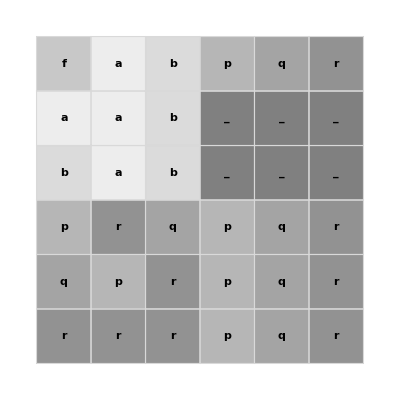

```mathematica
AFD = {{q,p,r},{a,b},{{q,a,p},{q,b,r},{p,a,r},{p,b,q},{r,a,r},{r,b,r}},q,{r}};
AFDtoAC[AFD]
```